## grow-example.nb

Example Cellzilla2D notebook illustrating: 
	grow
	SimAnimate
	LineageAnimate
Portions of this notebook’s output have been suppressed (removed) to save space for internet display. All of the input cells included are sufficient to recover the output shown. 

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<xlr8r.m;
<<Cellzilla2D.m;
```

xCellerator 0.95 (28-Feb-2014) loaded Fri 9 Jun 2017 18:00:23
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

Cellzilla2D (3.0.51c (08 June 2017)) loaded Fri 9 Jun 2017 18:00:23
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
$HistoryLength=1
```

1

### Generate A Template of 8 cells

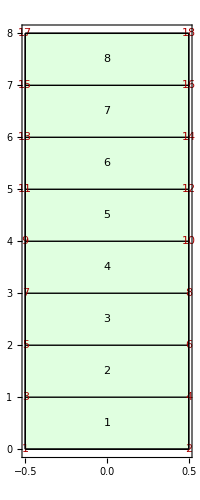

```mathematica
q=TemplateRectangular[{-1/2,1/2,1}, {0,8, 1}];
Q=Tissue2DTissue[q];
ShowTissue[Q,Frame-> True, "CellNumbers"-> True, "VertexNumbers"-> True]
```

### Define an internal pressure gradient in the template with the maximum in the second cell from the top and distributed via a bell curve

```mathematica
TC=Centroid[Q];
top=TissueVertices[Q][[18]];
f[i_]:=X[i]-> (BellCurve[1,top[[2]]-1.5,1.5][TC[[i,2]]]);
```

```mathematica
network={{∅->X,BellCurve[1, tip[2][t]-1.5,1.5][ycen[t]]}, {X-> ∅, 1}};
n=NTissueCells[Q];
centroids=Centroid[Q];
```

```mathematica
myic=f/@Range[n]
```

{X[1]→0.000335463,X[2]→0.00386592,X[3]→0.0285655,X[4]→0.135335,X[5]→0.411112,X[6]→0.800737,X[7]→1.,X[8]→0.800737}

```mathematica
MemoryInUse[]
```

120714800

```mathematica
MaxMemoryUsed[]
```

179091056

### run the simulation for 100,000 time units

```mathematica
SIM=grow[Q,0,100000,
"center"-> cen,
"L1Anticlinal"-> False,
"Intercellular"-> {}, 
"IC"-> myic, 
"Walls"-> False, 
"mumax"-> 1, "mumin"-> 1,"muMaxDegrees"-> 90.0,
"IsotropicGrowth"-> False, 
"kmin"-> 1, "kmax"->1, "kMaxDegrees"-> 0, 
"IsotropicSprings"-> False, 
"TestCase"-> "Grow-Example", 
"IgnoreDivisionRadius"-> Infinity, 
"MaxRadius"-> Infinity, 
"Reactions"-> network, 
"Pumps"-> {},
"Diffusion"-> {}, 
"WallReactions"->{},
"BoundaryConditions"-> {X-> 0}, 
"EdgeVariable"-> ell,
"CellVariable"-> area,
"Growing"-> True,
"Restlength"-> resting,
"k"-> {k, 1&}, 
"mu"-> {μ, .01(.1 + 10*(X[#1][t]+X[#2][t]))&},
"P"-> {P, .01*(.05+100*X[#][t])&}, 
"DivisionModel"-> "Errera",
"Parameters"-> {}, 
"DivisionThreshold"-> 1.1, 
"DivisionSigma"-> 0.10, 
"DivisionVariable"-> area, 
"MinAngleSpread"->135,
"Verbose"-> False, 
"Origin"-> {0, 0}, 
"ShowOptions"-> {Frame-> True,ImageSize-> 512, "CellNumbers"-> False, "EdgeNumbers"-> False, 
PlotRange-> {{-12.5,12.5}, {-5,25}}}
];
```

simdir = /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0001.png

Actual Clock Time:  | 09-Jun-2017-at-18:00:55
Memory in Use (GB):  | 0.150742
Max Memory Used (GB):  | 0.166792
Free Memory (GB):  | 0.191029

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 4 (static cell 4) divides at t = 107.105

Cell 6 (static cell 6) divides at t = 107.105

Cell 8 (static cell 8) divides at t = 107.105

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0002.png

Actual Clock Time:  | 09-Jun-2017-at-18:01:01
Memory in Use (GB):  | 0.158314
Max Memory Used (GB):  | 0.173783
Free Memory (GB):  | 0.174309
CPU Used(seconds):  | 6.35592
Number of Cells:  | 11
Cell Divisions:  | 3
Simulator Steps:  | 2
Number of Variables:  | 237

Cell Division Errera's Method

Cell Division Errera's Method

Cell 2 (static cell 2) divides at t = 136.399

Cell 7 (static cell 7) divides at t = 136.399

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0003.png

Actual Clock Time:  | 09-Jun-2017-at-18:01:06
Memory in Use (GB):  | 0.161092
Max Memory Used (GB):  | 0.176569
Free Memory (GB):  | 0.170261
CPU Used(seconds):  | 11.7906
Number of Cells:  | 13
Cell Divisions:  | 5
Simulator Steps:  | 3
Number of Variables:  | 321

Cell Division Errera's Method

Cell 5 (static cell 5) divides at t = 388.454

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0004.png

Actual Clock Time:  | 09-Jun-2017-at-18:01:12
Memory in Use (GB):  | 0.163576
Max Memory Used (GB):  | 0.179057
Free Memory (GB):  | 0.16711
CPU Used(seconds):  | 17.8735
Number of Cells:  | 14
Cell Divisions:  | 6
Simulator Steps:  | 4
Number of Variables:  | 377

Cell Division Errera's Method

Cell 3 (static cell 3) divides at t = 3926.49

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0005.png

Actual Clock Time:  | 09-Jun-2017-at-18:01:19
Memory in Use (GB):  | 0.173052
Max Memory Used (GB):  | 0.188536
Free Memory (GB):  | 0.155743
CPU Used(seconds):  | 25.5689
Number of Cells:  | 15
Cell Divisions:  | 7
Simulator Steps:  | 5
Number of Variables:  | 405

Cell Division Errera's Method

Cell 13 (static cell 13) divides at t = 5430.75

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0006.png

Actual Clock Time:  | 09-Jun-2017-at-18:01:32
Memory in Use (GB):  | 0.168539
Max Memory Used (GB):  | 0.188536
Free Memory (GB):  | 0.142536
CPU Used(seconds):  | 37.7216
Number of Cells:  | 16
Cell Divisions:  | 8
Simulator Steps:  | 6
Number of Variables:  | 433

Cell Division Errera's Method

Cell 7 (static cell 7) divides at t = 5656.29

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0007.png

Actual Clock Time:  | 09-Jun-2017-at-18:01:46
Memory in Use (GB):  | 0.171142
Max Memory Used (GB):  | 0.188536
Free Memory (GB):  | 0.142719
CPU Used(seconds):  | 51.071
Number of Cells:  | 17
Cell Divisions:  | 9
Simulator Steps:  | 7
Number of Variables:  | 461

Cell Division Errera's Method

Cell 10 (static cell 10) divides at t = 6445.9

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0008.png

Actual Clock Time:  | 09-Jun-2017-at-18:02:00
Memory in Use (GB):  | 0.174657
Max Memory Used (GB):  | 0.190152
Free Memory (GB):  | 0.112942
CPU Used(seconds):  | 64.3054
Number of Cells:  | 18
Cell Divisions:  | 10
Simulator Steps:  | 8
Number of Variables:  | 489

Cell Division Errera's Method

Cell Division Errera's Method

Cell 6 (static cell 6) divides at t = 6724.82

Cell 11 (static cell 11) divides at t = 6724.82

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0009.png

Actual Clock Time:  | 09-Jun-2017-at-18:02:19
Memory in Use (GB):  | 0.178265
Max Memory Used (GB):  | 0.193768
Free Memory (GB):  | 0.0773087
CPU Used(seconds):  | 82.8428
Number of Cells:  | 20
Cell Divisions:  | 12
Simulator Steps:  | 9
Number of Variables:  | 517

Cell Division Errera's Method

Cell 8 (static cell 8) divides at t = 10830.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0010.png

Actual Clock Time:  | 09-Jun-2017-at-18:02:36
Memory in Use (GB):  | 0.184535
Max Memory Used (GB):  | 0.200469
Free Memory (GB):  | 0.0731697
CPU Used(seconds):  | 100.061
Number of Cells:  | 21
Cell Divisions:  | 13
Simulator Steps:  | 10
Number of Variables:  | 573

Cell Division Errera's Method

Cell 13 (static cell 13) divides at t = 11616.1

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0011.png

Actual Clock Time:  | 09-Jun-2017-at-18:02:57
Memory in Use (GB):  | 0.184159
Max Memory Used (GB):  | 0.205232
Free Memory (GB):  | 0.075779
CPU Used(seconds):  | 119.303
Number of Cells:  | 22
Cell Divisions:  | 14
Simulator Steps:  | 11
Number of Variables:  | 601

Cell Division Errera's Method

Cell 17 (static cell 17) divides at t = 12247.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0012.png

Actual Clock Time:  | 09-Jun-2017-at-18:03:18
Memory in Use (GB):  | 0.187614
Max Memory Used (GB):  | 0.205867
Free Memory (GB):  | 0.0739708
CPU Used(seconds):  | 139.145
Number of Cells:  | 23
Cell Divisions:  | 15
Simulator Steps:  | 12
Number of Variables:  | 629

Cell Division Errera's Method

Cell Division Errera's Method

Cell 7 (static cell 7) divides at t = 12666.4

Cell 11 (static cell 11) divides at t = 12666.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0013.png

Actual Clock Time:  | 09-Jun-2017-at-18:03:45
Memory in Use (GB):  | 0.191444
Max Memory Used (GB):  | 0.210354
Free Memory (GB):  | 0.0859337
CPU Used(seconds):  | 164.101
Number of Cells:  | 25
Cell Divisions:  | 17
Simulator Steps:  | 13
Number of Variables:  | 657

Cell Division Errera's Method

Cell 16 (static cell 16) divides at t = 13320.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0014.png

Actual Clock Time:  | 09-Jun-2017-at-18:04:09
Memory in Use (GB):  | 0.195096
Max Memory Used (GB):  | 0.216396
Free Memory (GB):  | 0.0950317
CPU Used(seconds):  | 187.577
Number of Cells:  | 26
Cell Divisions:  | 18
Simulator Steps:  | 14
Number of Variables:  | 713

Cell Division Errera's Method

Cell 20 (static cell 20) divides at t = 14122.9

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0015.png

Actual Clock Time:  | 09-Jun-2017-at-18:04:35
Memory in Use (GB):  | 0.199653
Max Memory Used (GB):  | 0.221492
Free Memory (GB):  | 0.0463142
CPU Used(seconds):  | 211.915
Number of Cells:  | 27
Cell Divisions:  | 19
Simulator Steps:  | 15
Number of Variables:  | 741

Cell Division Errera's Method

Cell 8 (static cell 8) divides at t = 16376.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0016.png

Actual Clock Time:  | 09-Jun-2017-at-18:05:04
Memory in Use (GB):  | 0.206298
Max Memory Used (GB):  | 0.228589
Free Memory (GB):  | 0.0303955
CPU Used(seconds):  | 239.25
Number of Cells:  | 28
Cell Divisions:  | 20
Simulator Steps:  | 16
Number of Variables:  | 769

Cell Division Errera's Method

Cell 13 (static cell 13) divides at t = 18088.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0017.png

Actual Clock Time:  | 09-Jun-2017-at-18:05:33
Memory in Use (GB):  | 0.210332
Max Memory Used (GB):  | 0.234281
Free Memory (GB):  | 0.048317
CPU Used(seconds):  | 267.51
Number of Cells:  | 29
Cell Divisions:  | 21
Simulator Steps:  | 17
Number of Variables:  | 797

Cell Division Errera's Method

Cell 22 (static cell 22) divides at t = 18343.1

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0018.png

Actual Clock Time:  | 09-Jun-2017-at-18:06:02
Memory in Use (GB):  | 0.214796
Max Memory Used (GB):  | 0.239249
Free Memory (GB):  | 0.0602493
CPU Used(seconds):  | 295.867
Number of Cells:  | 30
Cell Divisions:  | 22
Simulator Steps:  | 18
Number of Variables:  | 825

Cell Division Errera's Method

Cell 26 (static cell 26) divides at t = 18485.7

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0019.png

Actual Clock Time:  | 09-Jun-2017-at-18:06:32
Memory in Use (GB):  | 0.218819
Max Memory Used (GB):  | 0.244819
Free Memory (GB):  | 0.0695877
CPU Used(seconds):  | 324.148
Number of Cells:  | 31
Cell Divisions:  | 23
Simulator Steps:  | 19
Number of Variables:  | 853

Cell Division Errera's Method

Cell 25 (static cell 25) divides at t = 18771.3

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0020.png

Actual Clock Time:  | 09-Jun-2017-at-18:07:14
Memory in Use (GB):  | 0.224255
Max Memory Used (GB):  | 0.249803
Free Memory (GB):  | 0.0537415
CPU Used(seconds):  | 358.581
Number of Cells:  | 32
Cell Divisions:  | 24
Simulator Steps:  | 20
Number of Variables:  | 881

Cell Division Errera's Method

Cell Division Errera's Method

Cell 11 (static cell 11) divides at t = 19727.1

Cell 27 (static cell 27) divides at t = 19727.1

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0021.png

Actual Clock Time:  | 09-Jun-2017-at-18:07:45
Memory in Use (GB):  | 0.229203
Max Memory Used (GB):  | 0.256322
Free Memory (GB):  | 0.0526962
CPU Used(seconds):  | 391.111
Number of Cells:  | 34
Cell Divisions:  | 26
Simulator Steps:  | 21
Number of Variables:  | 909

Cell Division Errera's Method

Cell Division Errera's Method

Cell 7 (static cell 7) divides at t = 20245.1

Cell 20 (static cell 20) divides at t = 20245.1

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0022.png

Actual Clock Time:  | 09-Jun-2017-at-18:08:06
Memory in Use (GB):  | 0.235322
Max Memory Used (GB):  | 0.26325
Free Memory (GB):  | 0.0571556
CPU Used(seconds):  | 413.076
Number of Cells:  | 36
Cell Divisions:  | 28
Simulator Steps:  | 22
Number of Variables:  | 965

Cell Division Errera's Method

Cell Division Errera's Method

Cell 19 (static cell 19) divides at t = 20892.8

Cell 21 (static cell 21) divides at t = 20892.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0023.png

Actual Clock Time:  | 09-Jun-2017-at-18:08:28
Memory in Use (GB):  | 0.241893
Max Memory Used (GB):  | 0.271419
Free Memory (GB):  | 0.0628929
CPU Used(seconds):  | 435.728
Number of Cells:  | 38
Cell Divisions:  | 30
Simulator Steps:  | 23
Number of Variables:  | 1021

Cell Division Errera's Method

Cell 8 (static cell 8) divides at t = 21764.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0024.png

Actual Clock Time:  | 09-Jun-2017-at-18:08:49
Memory in Use (GB):  | 0.246428
Max Memory Used (GB):  | 0.280004
Free Memory (GB):  | 0.0688515
CPU Used(seconds):  | 457.879
Number of Cells:  | 39
Cell Divisions:  | 31
Simulator Steps:  | 24
Number of Variables:  | 1077

Cell Division Errera's Method

Cell 16 (static cell 16) divides at t = 22182.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0025.png

Actual Clock Time:  | 09-Jun-2017-at-18:09:11
Memory in Use (GB):  | 0.252431
Max Memory Used (GB):  | 0.285511
Free Memory (GB):  | 0.0779953
CPU Used(seconds):  | 480.668
Number of Cells:  | 40
Cell Divisions:  | 32
Simulator Steps:  | 25
Number of Variables:  | 1105

Cell Division Errera's Method

Cell 23 (static cell 23) divides at t = 24136.5

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0026.png

Actual Clock Time:  | 09-Jun-2017-at-18:09:34
Memory in Use (GB):  | 0.260357
Max Memory Used (GB):  | 0.29354
Free Memory (GB):  | 0.122829
CPU Used(seconds):  | 504.654
Number of Cells:  | 41
Cell Divisions:  | 33
Simulator Steps:  | 26
Number of Variables:  | 1133

Cell Division Errera's Method

Cell 28 (static cell 28) divides at t = 24402.7

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0027.png

Actual Clock Time:  | 09-Jun-2017-at-18:09:57
Memory in Use (GB):  | 0.265809
Max Memory Used (GB):  | 0.30144
Free Memory (GB):  | 0.119755
CPU Used(seconds):  | 528.743
Number of Cells:  | 42
Cell Divisions:  | 34
Simulator Steps:  | 27
Number of Variables:  | 1161

Cell Division Errera's Method

Cell 38 (static cell 38) divides at t = 24977.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0028.png

Actual Clock Time:  | 09-Jun-2017-at-18:10:21
Memory in Use (GB):  | 0.272289
Max Memory Used (GB):  | 0.307997
Free Memory (GB):  | 0.114212
CPU Used(seconds):  | 553.757
Number of Cells:  | 43
Cell Divisions:  | 35
Simulator Steps:  | 28
Number of Variables:  | 1189

Cell Division Errera's Method

Cell 17 (static cell 17) divides at t = 26772.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0029.png

Actual Clock Time:  | 09-Jun-2017-at-18:10:46
Memory in Use (GB):  | 0.284037
Max Memory Used (GB):  | 0.319331
Free Memory (GB):  | 0.101376
CPU Used(seconds):  | 579.
Number of Cells:  | 44
Cell Divisions:  | 36
Simulator Steps:  | 29
Number of Variables:  | 1217

Cell Division Errera's Method

Cell 32 (static cell 32) divides at t = 27014.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0030.png

Actual Clock Time:  | 09-Jun-2017-at-18:11:11
Memory in Use (GB):  | 0.289054
Max Memory Used (GB):  | 0.328226
Free Memory (GB):  | 0.118797
CPU Used(seconds):  | 604.536
Number of Cells:  | 45
Cell Divisions:  | 37
Simulator Steps:  | 30
Number of Variables:  | 1245

Cell Division Errera's Method

Cell 27 (static cell 27) divides at t = 27232.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0031.png

Actual Clock Time:  | 09-Jun-2017-at-18:11:37
Memory in Use (GB):  | 0.295972
Max Memory Used (GB):  | 0.334325
Free Memory (GB):  | 0.113739
CPU Used(seconds):  | 631.853
Number of Cells:  | 46
Cell Divisions:  | 38
Simulator Steps:  | 31
Number of Variables:  | 1273

Cell Division Errera's Method

Cell 20 (static cell 20) divides at t = 27537.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0032.png

Actual Clock Time:  | 09-Jun-2017-at-18:12:04
Memory in Use (GB):  | 0.302494
Max Memory Used (GB):  | 0.342334
Free Memory (GB):  | 0.116776
CPU Used(seconds):  | 659.578
Number of Cells:  | 47
Cell Divisions:  | 39
Simulator Steps:  | 32
Number of Variables:  | 1301

Cell Division Errera's Method

Cell Division Errera's Method

Cell 24 (static cell 24) divides at t = 27705.8

Cell 25 (static cell 25) divides at t = 27705.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0033.png

Actual Clock Time:  | 09-Jun-2017-at-18:12:39
Memory in Use (GB):  | 0.30904
Max Memory Used (GB):  | 0.349845
Free Memory (GB):  | 0.104137
CPU Used(seconds):  | 694.788
Number of Cells:  | 49
Cell Divisions:  | 41
Simulator Steps:  | 33
Number of Variables:  | 1329

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 18 (static cell 18) divides at t = 27930.

Cell 22 (static cell 22) divides at t = 27930.

Cell 29 (static cell 29) divides at t = 27930.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0034.png

Actual Clock Time:  | 09-Jun-2017-at-18:13:23
Memory in Use (GB):  | 0.318645
Max Memory Used (GB):  | 0.358797
Free Memory (GB):  | 0.0262947
CPU Used(seconds):  | 736.671
Number of Cells:  | 52
Cell Divisions:  | 44
Simulator Steps:  | 34
Number of Variables:  | 1385

Cell Division Errera's Method

Cell 36 (static cell 36) divides at t = 28152.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0035.png

Actual Clock Time:  | 09-Jun-2017-at-18:14:04
Memory in Use (GB):  | 0.32756
Max Memory Used (GB):  | 0.37138
Free Memory (GB):  | 0.0568886
CPU Used(seconds):  | 774.966
Number of Cells:  | 53
Cell Divisions:  | 45
Simulator Steps:  | 35
Number of Variables:  | 1469

Cell Division Errera's Method

Cell Division Errera's Method

Cell 11 (static cell 11) divides at t = 28291.1

Cell 39 (static cell 39) divides at t = 28291.1

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0036.png

Actual Clock Time:  | 09-Jun-2017-at-18:14:49
Memory in Use (GB):  | 0.334563
Max Memory Used (GB):  | 0.381221
Free Memory (GB):  | 0.095417
CPU Used(seconds):  | 816.735
Number of Cells:  | 55
Cell Divisions:  | 47
Simulator Steps:  | 36
Number of Variables:  | 1497

Cell Division Errera's Method

Cell 21 (static cell 21) divides at t = 28523.3

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0037.png

Actual Clock Time:  | 09-Jun-2017-at-18:15:33
Memory in Use (GB):  | 0.343093
Max Memory Used (GB):  | 0.390341
Free Memory (GB):  | 0.0498581
CPU Used(seconds):  | 857.78
Number of Cells:  | 56
Cell Divisions:  | 48
Simulator Steps:  | 37
Number of Variables:  | 1553

Cell Division Errera's Method

Cell 8 (static cell 8) divides at t = 29222.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0038.png

Actual Clock Time:  | 09-Jun-2017-at-18:16:21
Memory in Use (GB):  | 0.352147
Max Memory Used (GB):  | 0.399823
Free Memory (GB):  | 0.0425224
CPU Used(seconds):  | 901.769
Number of Cells:  | 57
Cell Divisions:  | 49
Simulator Steps:  | 38
Number of Variables:  | 1581

Cell Division Errera's Method

Cell 31 (static cell 31) divides at t = 30421.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0039.png

Actual Clock Time:  | 09-Jun-2017-at-18:17:09
Memory in Use (GB):  | 0.360362
Max Memory Used (GB):  | 0.410067
Free Memory (GB):  | 0.0555992
CPU Used(seconds):  | 946.844
Number of Cells:  | 58
Cell Divisions:  | 50
Simulator Steps:  | 39
Number of Variables:  | 1609

Cell Division Errera's Method

Cell 40 (static cell 40) divides at t = 30775.5

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0040.png

Actual Clock Time:  | 09-Jun-2017-at-18:18:00
Memory in Use (GB):  | 0.368025
Max Memory Used (GB):  | 0.419278
Free Memory (GB):  | 0.0483208
CPU Used(seconds):  | 990.986
Number of Cells:  | 59
Cell Divisions:  | 51
Simulator Steps:  | 40
Number of Variables:  | 1637

Cell Division Errera's Method

Cell 33 (static cell 33) divides at t = 31046.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0041.png

Actual Clock Time:  | 09-Jun-2017-at-18:18:54
Memory in Use (GB):  | 0.380806
Max Memory Used (GB):  | 0.430011
Free Memory (GB):  | 0.0165749
CPU Used(seconds):  | 1038.82
Number of Cells:  | 60
Cell Divisions:  | 52
Simulator Steps:  | 41
Number of Variables:  | 1665

Cell Division Errera's Method

Cell Division Errera's Method

Cell 28 (static cell 28) divides at t = 31642.5

Cell 42 (static cell 42) divides at t = 31642.5

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0042.png

Actual Clock Time:  | 09-Jun-2017-at-18:19:48
Memory in Use (GB):  | 0.39015
Max Memory Used (GB):  | 0.441911
Free Memory (GB):  | 0.0668106
CPU Used(seconds):  | 1090.59
Number of Cells:  | 62
Cell Divisions:  | 54
Simulator Steps:  | 42
Number of Variables:  | 1693

Cell Division Errera's Method

Cell Division Errera's Method

Cell 34 (static cell 34) divides at t = 31802.3

Cell 38 (static cell 38) divides at t = 31802.3

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0043.png

Actual Clock Time:  | 09-Jun-2017-at-18:20:48
Memory in Use (GB):  | 0.400591
Max Memory Used (GB):  | 0.453397
Free Memory (GB):  | 0.055275
CPU Used(seconds):  | 1147.89
Number of Cells:  | 64
Cell Divisions:  | 56
Simulator Steps:  | 43
Number of Variables:  | 1749

Cell Division Errera's Method

Cell 43 (static cell 43) divides at t = 34500.9

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0044.png

Actual Clock Time:  | 09-Jun-2017-at-18:21:45
Memory in Use (GB):  | 0.412115
Max Memory Used (GB):  | 0.466007
Free Memory (GB):  | 0.0606804
CPU Used(seconds):  | 1201.35
Number of Cells:  | 65
Cell Divisions:  | 57
Simulator Steps:  | 44
Number of Variables:  | 1805

Cell Division Errera's Method

Cell 39 (static cell 39) divides at t = 34757.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0045.png

Actual Clock Time:  | 09-Jun-2017-at-18:22:41
Memory in Use (GB):  | 0.418287
Max Memory Used (GB):  | 0.478322
Free Memory (GB):  | 0.0576096
CPU Used(seconds):  | 1254.36
Number of Cells:  | 66
Cell Divisions:  | 58
Simulator Steps:  | 45
Number of Variables:  | 1833

Cell Division Errera's Method

Cell 21 (static cell 21) divides at t = 35009.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0046.png

Actual Clock Time:  | 09-Jun-2017-at-18:23:40
Memory in Use (GB):  | 0.437778
Max Memory Used (GB):  | 0.493353
Free Memory (GB):  | 0.0774117
CPU Used(seconds):  | 1309.91
Number of Cells:  | 67
Cell Divisions:  | 59
Simulator Steps:  | 46
Number of Variables:  | 1861

Cell Division Errera's Method

Cell 55 (static cell 55) divides at t = 35830.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0047.png

Actual Clock Time:  | 09-Jun-2017-at-18:24:42
Memory in Use (GB):  | 0.44601
Max Memory Used (GB):  | 0.506082
Free Memory (GB):  | 0.100422
CPU Used(seconds):  | 1367.15
Number of Cells:  | 68
Cell Divisions:  | 60
Simulator Steps:  | 47
Number of Variables:  | 1889

Cell Division Errera's Method

Cell Division Errera's Method

Cell 45 (static cell 45) divides at t = 36005.5

Cell 56 (static cell 56) divides at t = 36005.5

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0048.png

Actual Clock Time:  | 09-Jun-2017-at-18:25:45
Memory in Use (GB):  | 0.457834
Max Memory Used (GB):  | 0.515365
Free Memory (GB):  | 0.0917435
CPU Used(seconds):  | 1428.35
Number of Cells:  | 70
Cell Divisions:  | 62
Simulator Steps:  | 48
Number of Variables:  | 1917

Cell Division Errera's Method

Cell 8 (static cell 8) divides at t = 36397.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0049.png

Actual Clock Time:  | 09-Jun-2017-at-18:26:47
Memory in Use (GB):  | 0.469405
Max Memory Used (GB):  | 0.529333
Free Memory (GB):  | 0.182507
CPU Used(seconds):  | 1488.04
Number of Cells:  | 71
Cell Divisions:  | 63
Simulator Steps:  | 49
Number of Variables:  | 1973

Cell Division Errera's Method

Cell 38 (static cell 38) divides at t = 36908.3

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0050.png

Actual Clock Time:  | 09-Jun-2017-at-18:27:51
Memory in Use (GB):  | 0.478079
Max Memory Used (GB):  | 0.541913
Free Memory (GB):  | 0.202755
CPU Used(seconds):  | 1549.01
Number of Cells:  | 72
Cell Divisions:  | 64
Simulator Steps:  | 50
Number of Variables:  | 2001

Cell Division Errera's Method

Cell 30 (static cell 30) divides at t = 37516.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0051.png

Actual Clock Time:  | 09-Jun-2017-at-18:28:59
Memory in Use (GB):  | 0.48824
Max Memory Used (GB):  | 0.551519
Free Memory (GB):  | 0.163425
CPU Used(seconds):  | 1611.19
Number of Cells:  | 73
Cell Divisions:  | 65
Simulator Steps:  | 51
Number of Variables:  | 2029

Cell Division Errera's Method

Cell Division Errera's Method

Cell 11 (static cell 11) divides at t = 37792.2

Cell 13 (static cell 13) divides at t = 37792.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0052.png

Actual Clock Time:  | 09-Jun-2017-at-18:30:10
Memory in Use (GB):  | 0.501605
Max Memory Used (GB):  | 0.562763
Free Memory (GB):  | 0.194191
CPU Used(seconds):  | 1680.3
Number of Cells:  | 75
Cell Divisions:  | 67
Simulator Steps:  | 52
Number of Variables:  | 2057

Cell Division Errera's Method

Cell 60 (static cell 60) divides at t = 38610.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0053.png

Actual Clock Time:  | 09-Jun-2017-at-18:31:20
Memory in Use (GB):  | 0.513351
Max Memory Used (GB):  | 0.578276
Free Memory (GB):  | 0.160275
CPU Used(seconds):  | 1746.84
Number of Cells:  | 76
Cell Divisions:  | 68
Simulator Steps:  | 53
Number of Variables:  | 2113

Cell Division Errera's Method

Cell 42 (static cell 42) divides at t = 38870.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0054.png

Actual Clock Time:  | 09-Jun-2017-at-18:32:32
Memory in Use (GB):  | 0.523736
Max Memory Used (GB):  | 0.591048
Free Memory (GB):  | 0.150944
CPU Used(seconds):  | 1814.48
Number of Cells:  | 77
Cell Divisions:  | 69
Simulator Steps:  | 54
Number of Variables:  | 2141

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 33 (static cell 33) divides at t = 39009.5

Cell 46 (static cell 46) divides at t = 39009.5

Cell 57 (static cell 57) divides at t = 39009.5

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0055.png

Actual Clock Time:  | 09-Jun-2017-at-18:33:49
Memory in Use (GB):  | 0.535149
Max Memory Used (GB):  | 0.602547
Free Memory (GB):  | 0.111069
CPU Used(seconds):  | 1888.65
Number of Cells:  | 80
Cell Divisions:  | 72
Simulator Steps:  | 55
Number of Variables:  | 2169

Cell Division Errera's Method

Cell 27 (static cell 27) divides at t = 39506.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0056.png

Actual Clock Time:  | 09-Jun-2017-at-18:35:08
Memory in Use (GB):  | 0.550148
Max Memory Used (GB):  | 0.617042
Free Memory (GB):  | 0.140327
CPU Used(seconds):  | 1964.98
Number of Cells:  | 81
Cell Divisions:  | 73
Simulator Steps:  | 56
Number of Variables:  | 2253

Cell Division Errera's Method

Cell 64 (static cell 64) divides at t = 39621.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0057.png

Actual Clock Time:  | 09-Jun-2017-at-18:36:31
Memory in Use (GB):  | 0.561655
Max Memory Used (GB):  | 0.632997
Free Memory (GB):  | 0.0808792
CPU Used(seconds):  | 2041.93
Number of Cells:  | 82
Cell Divisions:  | 74
Simulator Steps:  | 57
Number of Variables:  | 2281

Cell Division Errera's Method

Cell 65 (static cell 65) divides at t = 40510.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0058.png

Actual Clock Time:  | 09-Jun-2017-at-18:37:54
Memory in Use (GB):  | 0.573216
Max Memory Used (GB):  | 0.645512
Free Memory (GB):  | 0.0881729
CPU Used(seconds):  | 2121.57
Number of Cells:  | 83
Cell Divisions:  | 75
Simulator Steps:  | 58
Number of Variables:  | 2309

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 14 (static cell 14) divides at t = 40831.6

Cell 32 (static cell 32) divides at t = 40831.6

Cell 39 (static cell 39) divides at t = 40831.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0059.png

Actual Clock Time:  | 09-Jun-2017-at-18:39:25
Memory in Use (GB):  | 0.587504
Max Memory Used (GB):  | 0.658148
Free Memory (GB):  | 0.109921
CPU Used(seconds):  | 2209.95
Number of Cells:  | 86
Cell Divisions:  | 78
Simulator Steps:  | 59
Number of Variables:  | 2337

Cell Division Errera's Method

Cell Division Errera's Method

Cell 54 (static cell 54) divides at t = 41388.

Cell 68 (static cell 68) divides at t = 41388.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0060.png

Actual Clock Time:  | 09-Jun-2017-at-18:41:01
Memory in Use (GB):  | 0.601804
Max Memory Used (GB):  | 0.67561
Free Memory (GB):  | 0.0729179
CPU Used(seconds):  | 2304.05
Number of Cells:  | 88
Cell Divisions:  | 80
Simulator Steps:  | 60
Number of Variables:  | 2421

Cell Division Errera's Method

Cell Division Errera's Method

Cell 47 (static cell 47) divides at t = 41668.7

Cell 62 (static cell 62) divides at t = 41668.7

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0061.png

Actual Clock Time:  | 09-Jun-2017-at-18:42:38
Memory in Use (GB):  | 0.618383
Max Memory Used (GB):  | 0.695887
Free Memory (GB):  | 0.140484
CPU Used(seconds):  | 2398.93
Number of Cells:  | 90
Cell Divisions:  | 82
Simulator Steps:  | 61
Number of Variables:  | 2477

Cell Division Errera's Method

Cell 66 (static cell 66) divides at t = 41913.7

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0062.png

Actual Clock Time:  | 09-Jun-2017-at-18:44:17
Memory in Use (GB):  | 0.632898
Max Memory Used (GB):  | 0.711452
Free Memory (GB):  | 0.115211
CPU Used(seconds):  | 2495.7
Number of Cells:  | 91
Cell Divisions:  | 83
Simulator Steps:  | 62
Number of Variables:  | 2533

Cell Division Errera's Method

Cell 72 (static cell 72) divides at t = 42515.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0063.png

Actual Clock Time:  | 09-Jun-2017-at-18:45:58
Memory in Use (GB):  | 0.64595
Max Memory Used (GB):  | 0.726178
Free Memory (GB):  | 0.0783234
CPU Used(seconds):  | 2595.36
Number of Cells:  | 92
Cell Divisions:  | 84
Simulator Steps:  | 63
Number of Variables:  | 2561

Cell Division Errera's Method

Cell Division Errera's Method

Cell 26 (static cell 26) divides at t = 42835.6

Cell 38 (static cell 38) divides at t = 42835.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0064.png

Actual Clock Time:  | 09-Jun-2017-at-18:47:53
Memory in Use (GB):  | 0.660061
Max Memory Used (GB):  | 0.740386
Free Memory (GB):  | 0.15493
CPU Used(seconds):  | 2708.76
Number of Cells:  | 94
Cell Divisions:  | 86
Simulator Steps:  | 64
Number of Variables:  | 2589

Cell Division Errera's Method

Cell 56 (static cell 56) divides at t = 43896.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0065.png

Actual Clock Time:  | 09-Jun-2017-at-18:49:40
Memory in Use (GB):  | 0.677261
Max Memory Used (GB):  | 0.756448
Free Memory (GB):  | 0.132088
CPU Used(seconds):  | 2813.08
Number of Cells:  | 95
Cell Divisions:  | 87
Simulator Steps:  | 65
Number of Variables:  | 2645

Cell Division Errera's Method

Cell 70 (static cell 70) divides at t = 44549.3

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0066.png

Actual Clock Time:  | 09-Jun-2017-at-18:51:28
Memory in Use (GB):  | 0.686457
Max Memory Used (GB):  | 0.77474
Free Memory (GB):  | 0.0787468
CPU Used(seconds):  | 2918.58
Number of Cells:  | 96
Cell Divisions:  | 88
Simulator Steps:  | 66
Number of Variables:  | 2673

Cell Division Errera's Method

Cell 8 (static cell 8) divides at t = 44715.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0067.png

Actual Clock Time:  | 09-Jun-2017-at-18:53:19
Memory in Use (GB):  | 0.701834
Max Memory Used (GB):  | 0.784763
Free Memory (GB):  | 0.105968
CPU Used(seconds):  | 3026.2
Number of Cells:  | 97
Cell Divisions:  | 89
Simulator Steps:  | 67
Number of Variables:  | 2701

Cell Division Errera's Method

Cell 71 (static cell 71) divides at t = 45148.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0068.png

Actual Clock Time:  | 09-Jun-2017-at-18:55:15
Memory in Use (GB):  | 0.718814
Max Memory Used (GB):  | 0.801138
Free Memory (GB):  | 0.0948753
CPU Used(seconds):  | 3137.86
Number of Cells:  | 98
Cell Divisions:  | 90
Simulator Steps:  | 68
Number of Variables:  | 2729

Cell Division Errera's Method

Cell Division Errera's Method

Cell 29 (static cell 29) divides at t = 45785.9

Cell 55 (static cell 55) divides at t = 45785.9

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0069.png

Actual Clock Time:  | 09-Jun-2017-at-18:57:14
Memory in Use (GB):  | 0.749832
Max Memory Used (GB):  | 0.834893
Free Memory (GB):  | 0.102592
CPU Used(seconds):  | 3256.95
Number of Cells:  | 100
Cell Divisions:  | 92
Simulator Steps:  | 69
Number of Variables:  | 2757

Cell Division Errera's Method

Cell 28 (static cell 28) divides at t = 47571.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0070.png

Actual Clock Time:  | 09-Jun-2017-at-18:59:16
Memory in Use (GB):  | 0.767063
Max Memory Used (GB):  | 0.852508
Free Memory (GB):  | 0.105976
CPU Used(seconds):  | 3376.53
Number of Cells:  | 101
Cell Divisions:  | 93
Simulator Steps:  | 70
Number of Variables:  | 2813

Cell Division Errera's Method

Cell 39 (static cell 39) divides at t = 47779.7

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0071.png

Actual Clock Time:  | 09-Jun-2017-at-19:01:19
Memory in Use (GB):  | 0.781503
Max Memory Used (GB):  | 0.870714
Free Memory (GB):  | 0.092701
CPU Used(seconds):  | 3495.67
Number of Cells:  | 102
Cell Divisions:  | 94
Simulator Steps:  | 71
Number of Variables:  | 2841

Cell Division Errera's Method

Cell Division Errera's Method

Cell 78 (static cell 78) divides at t = 48055.7

Cell 82 (static cell 82) divides at t = 48055.7

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0072.png

Actual Clock Time:  | 09-Jun-2017-at-19:03:30
Memory in Use (GB):  | 0.793784
Max Memory Used (GB):  | 0.886289
Free Memory (GB):  | 0.0797615
CPU Used(seconds):  | 3625.07
Number of Cells:  | 104
Cell Divisions:  | 96
Simulator Steps:  | 72
Number of Variables:  | 2869

Cell Division Errera's Method

Cell 72 (static cell 72) divides at t = 48244.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0073.png

Actual Clock Time:  | 09-Jun-2017-at-19:05:41
Memory in Use (GB):  | 0.81074
Max Memory Used (GB):  | 0.900669
Free Memory (GB):  | 0.136631
CPU Used(seconds):  | 3751.87
Number of Cells:  | 105
Cell Divisions:  | 97
Simulator Steps:  | 73
Number of Variables:  | 2925

Cell Division Errera's Method

Cell 66 (static cell 66) divides at t = 48505.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0074.png

Actual Clock Time:  | 09-Jun-2017-at-19:07:53
Memory in Use (GB):  | 0.823983
Max Memory Used (GB):  | 0.918752
Free Memory (GB):  | 0.109364
CPU Used(seconds):  | 3880.15
Number of Cells:  | 106
Cell Divisions:  | 98
Simulator Steps:  | 74
Number of Variables:  | 2953

Cell Division Errera's Method

Cell 62 (static cell 62) divides at t = 48774.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0075.png

Actual Clock Time:  | 09-Jun-2017-at-19:10:04
Memory in Use (GB):  | 0.842609
Max Memory Used (GB):  | 0.932781
Free Memory (GB):  | 0.103088
CPU Used(seconds):  | 4009.8
Number of Cells:  | 107
Cell Divisions:  | 99
Simulator Steps:  | 75
Number of Variables:  | 2981

Cell Division Errera's Method

Cell 86 (static cell 86) divides at t = 49156.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0076.png

Actual Clock Time:  | 09-Jun-2017-at-19:12:18
Memory in Use (GB):  | 0.857828
Max Memory Used (GB):  | 0.952482
Free Memory (GB):  | 0.122864
CPU Used(seconds):  | 4140.95
Number of Cells:  | 108
Cell Divisions:  | 100
Simulator Steps:  | 76
Number of Variables:  | 3009

Cell Division Errera's Method

Cell Division Errera's Method

Cell 64 (static cell 64) divides at t = 49370.8

Cell 91 (static cell 91) divides at t = 49370.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0077.png

Actual Clock Time:  | 09-Jun-2017-at-19:14:44
Memory in Use (GB):  | 0.876256
Max Memory Used (GB):  | 0.968599
Free Memory (GB):  | 0.197018
CPU Used(seconds):  | 4285.92
Number of Cells:  | 110
Cell Divisions:  | 102
Simulator Steps:  | 77
Number of Variables:  | 3037

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 58 (static cell 58) divides at t = 49460.8

Cell 80 (static cell 80) divides at t = 49460.8

Cell 88 (static cell 88) divides at t = 49460.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0078.png

Actual Clock Time:  | 09-Jun-2017-at-19:17:13
Memory in Use (GB):  | 0.891999
Max Memory Used (GB):  | 0.989261
Free Memory (GB):  | 0.17794
CPU Used(seconds):  | 4432.48
Number of Cells:  | 113
Cell Divisions:  | 105
Simulator Steps:  | 78
Number of Variables:  | 3093

Cell Division Errera's Method

Cell 92 (static cell 92) divides at t = 49613.3

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0079.png

Actual Clock Time:  | 09-Jun-2017-at-19:19:47
Memory in Use (GB):  | 0.911891
Max Memory Used (GB):  | 1.00823
Free Memory (GB):  | 0.142761
CPU Used(seconds):  | 4581.89
Number of Cells:  | 114
Cell Divisions:  | 106
Simulator Steps:  | 79
Number of Variables:  | 3177

Cell Division Errera's Method

Cell 90 (static cell 90) divides at t = 49754.5

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0080.png

Actual Clock Time:  | 09-Jun-2017-at-19:22:20
Memory in Use (GB):  | 0.92454
Max Memory Used (GB):  | 1.02927
Free Memory (GB):  | 0.090416
CPU Used(seconds):  | 4729.15
Number of Cells:  | 115
Cell Divisions:  | 107
Simulator Steps:  | 80
Number of Variables:  | 3205

Cell Division Errera's Method

Cell 67 (static cell 67) divides at t = 51251.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0081.png

Actual Clock Time:  | 09-Jun-2017-at-19:24:58
Memory in Use (GB):  | 0.945648
Max Memory Used (GB):  | 1.0428
Free Memory (GB):  | 0.149521
CPU Used(seconds):  | 4883.44
Number of Cells:  | 116
Cell Divisions:  | 108
Simulator Steps:  | 81
Number of Variables:  | 3233

Cell Division Errera's Method

Cell 38 (static cell 38) divides at t = 51630.3

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0082.png

Actual Clock Time:  | 09-Jun-2017-at-19:27:39
Memory in Use (GB):  | 0.963489
Max Memory Used (GB):  | 1.06479
Free Memory (GB):  | 0.264565
CPU Used(seconds):  | 5039.58
Number of Cells:  | 117
Cell Divisions:  | 109
Simulator Steps:  | 82
Number of Variables:  | 3261

Cell Division Errera's Method

Cell Division Errera's Method

Cell 68 (static cell 68) divides at t = 52160.4

Cell 96 (static cell 96) divides at t = 52160.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0083.png

Actual Clock Time:  | 09-Jun-2017-at-19:30:28
Memory in Use (GB):  | 0.979579
Max Memory Used (GB):  | 1.08385
Free Memory (GB):  | 0.334564
CPU Used(seconds):  | 5210.04
Number of Cells:  | 119
Cell Divisions:  | 111
Simulator Steps:  | 83
Number of Variables:  | 3289

Cell Division Errera's Method

Cell Division Errera's Method

Cell 70 (static cell 70) divides at t = 53072.6

Cell 94 (static cell 94) divides at t = 53072.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0084.png

Actual Clock Time:  | 09-Jun-2017-at-19:33:31
Memory in Use (GB):  | 1.00088
Max Memory Used (GB):  | 1.10199
Free Memory (GB):  | 0.338413
CPU Used(seconds):  | 5395.96
Number of Cells:  | 121
Cell Divisions:  | 113
Simulator Steps:  | 84
Number of Variables:  | 3345

Cell Division Errera's Method

Cell Division Errera's Method

Cell 20 (static cell 20) divides at t = 53570.8

Cell 97 (static cell 97) divides at t = 53570.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0085.png

Actual Clock Time:  | 09-Jun-2017-at-19:36:37
Memory in Use (GB):  | 1.01822
Max Memory Used (GB):  | 1.1254
Free Memory (GB):  | 0.210705
CPU Used(seconds):  | 5578.28
Number of Cells:  | 123
Cell Divisions:  | 115
Simulator Steps:  | 85
Number of Variables:  | 3401

Cell Division Errera's Method

Cell 95 (static cell 95) divides at t = 54159.9

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0086.png

Actual Clock Time:  | 09-Jun-2017-at-19:39:47
Memory in Use (GB):  | 1.03569
Max Memory Used (GB):  | 1.14481
Free Memory (GB):  | 0.166229
CPU Used(seconds):  | 5765.05
Number of Cells:  | 124
Cell Divisions:  | 116
Simulator Steps:  | 86
Number of Variables:  | 3457

Cell Division Errera's Method

Cell 8 (static cell 8) divides at t = 54588.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0087.png

Actual Clock Time:  | 09-Jun-2017-at-19:43:07
Memory in Use (GB):  | 1.05433
Max Memory Used (GB):  | 1.1633
Free Memory (GB):  | 0.1106
CPU Used(seconds):  | 5959.61
Number of Cells:  | 125
Cell Divisions:  | 117
Simulator Steps:  | 87
Number of Variables:  | 3485

Cell Division Errera's Method

Cell Division Errera's Method

Cell 61 (static cell 61) divides at t = 55618.6

Cell 72 (static cell 72) divides at t = 55618.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0088.png

Actual Clock Time:  | 09-Jun-2017-at-19:46:26
Memory in Use (GB):  | 1.0761
Max Memory Used (GB):  | 1.18296
Free Memory (GB):  | 0.112122
CPU Used(seconds):  | 6158.59
Number of Cells:  | 127
Cell Divisions:  | 119
Simulator Steps:  | 88
Number of Variables:  | 3513

Cell Division Errera's Method

Cell Division Errera's Method

Cell 66 (static cell 66) divides at t = 55754.

Cell 106 (static cell 106) divides at t = 55754.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0089.png

Actual Clock Time:  | 09-Jun-2017-at-19:49:52
Memory in Use (GB):  | 1.10044
Max Memory Used (GB):  | 1.21486
Free Memory (GB):  | 0.198338
CPU Used(seconds):  | 6363.81
Number of Cells:  | 129
Cell Divisions:  | 121
Simulator Steps:  | 89
Number of Variables:  | 3569

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 1 (static cell 1) divides at t = 56199.7

Cell 21 (static cell 21) divides at t = 56199.7

Cell 39 (static cell 39) divides at t = 56199.7

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0090.png

Actual Clock Time:  | 09-Jun-2017-at-19:53:17
Memory in Use (GB):  | 1.12235
Max Memory Used (GB):  | 1.2339
Free Memory (GB):  | 0.168793
CPU Used(seconds):  | 6569.32
Number of Cells:  | 132
Cell Divisions:  | 124
Simulator Steps:  | 90
Number of Variables:  | 3625

Cell Division Errera's Method

Cell 105 (static cell 105) divides at t = 56679.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0091.png

Actual Clock Time:  | 09-Jun-2017-at-19:56:45
Memory in Use (GB):  | 1.14235
Max Memory Used (GB):  | 1.25841
Free Memory (GB):  | 0.160542
CPU Used(seconds):  | 6774.11
Number of Cells:  | 133
Cell Divisions:  | 125
Simulator Steps:  | 91
Number of Variables:  | 3709

Cell Division Errera's Method

Cell Division Errera's Method

Cell 43 (static cell 43) divides at t = 57063.3

Cell 62 (static cell 62) divides at t = 57063.3

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0092.png

Actual Clock Time:  | 09-Jun-2017-at-20:00:13
Memory in Use (GB):  | 1.16124
Max Memory Used (GB):  | 1.27947
Free Memory (GB):  | 0.196671
CPU Used(seconds):  | 6980.63
Number of Cells:  | 135
Cell Divisions:  | 127
Simulator Steps:  | 92
Number of Variables:  | 3737

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«1 more identical outputs»

Cell 60 (static cell 60) divides at t = 57292.6

Cell 65 (static cell 65) divides at t = 57292.6

Cell 83 (static cell 83) divides at t = 57292.6

Cell 114 (static cell 114) divides at t = 57292.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0093.png

Actual Clock Time:  | 09-Jun-2017-at-20:04:01
Memory in Use (GB):  | 1.18338
Max Memory Used (GB):  | 1.30027
Free Memory (GB):  | 0.0645943
CPU Used(seconds):  | 7208.58
Number of Cells:  | 139
Cell Divisions:  | 131
Simulator Steps:  | 93
Number of Variables:  | 3793

Cell Division Errera's Method

Cell Division Errera's Method

Cell 25 (static cell 25) divides at t = 58044.9

Cell 92 (static cell 92) divides at t = 58044.9

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0094.png

Actual Clock Time:  | 09-Jun-2017-at-20:07:49
Memory in Use (GB):  | 1.2065
Max Memory Used (GB):  | 1.3269
Free Memory (GB):  | 0.154156
CPU Used(seconds):  | 7439.
Number of Cells:  | 141
Cell Divisions:  | 133
Simulator Steps:  | 94
Number of Variables:  | 3905

Cell Division Errera's Method

Cell 110 (static cell 110) divides at t = 58286.3

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0095.png

Actual Clock Time:  | 09-Jun-2017-at-20:10:35
Memory in Use (GB):  | 1.2251
Max Memory Used (GB):  | 1.35194
Free Memory (GB):  | 0.156712
CPU Used(seconds):  | 7613.05
Number of Cells:  | 142
Cell Divisions:  | 134
Simulator Steps:  | 95
Number of Variables:  | 3961

Cell Division Errera's Method

Cell 107 (static cell 107) divides at t = 58924.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0096.png

Actual Clock Time:  | 09-Jun-2017-at-20:13:45
Memory in Use (GB):  | 1.24785
Max Memory Used (GB):  | 1.37133
Free Memory (GB):  | 0.0788002
CPU Used(seconds):  | 7805.96
Number of Cells:  | 143
Cell Divisions:  | 135
Simulator Steps:  | 96
Number of Variables:  | 3989

Cell Division Errera's Method

Cell 121 (static cell 121) divides at t = 59085.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0097.png

Actual Clock Time:  | 09-Jun-2017-at-20:17:14
Memory in Use (GB):  | 1.26512
Max Memory Used (GB):  | 1.39516
Free Memory (GB):  | 0.133526
CPU Used(seconds):  | 8019.61
Number of Cells:  | 144
Cell Divisions:  | 136
Simulator Steps:  | 97
Number of Variables:  | 4017

Cell Division Errera's Method

Cell 88 (static cell 88) divides at t = 59625.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0098.png

Actual Clock Time:  | 09-Jun-2017-at-20:20:43
Memory in Use (GB):  | 1.28822
Max Memory Used (GB):  | 1.41359
Free Memory (GB):  | 0.0858612
CPU Used(seconds):  | 8232.83
Number of Cells:  | 145
Cell Divisions:  | 137
Simulator Steps:  | 98
Number of Variables:  | 4045

Cell Division Errera's Method

Cell Division Errera's Method

Cell 90 (static cell 90) divides at t = 59968.2

Cell 104 (static cell 104) divides at t = 59968.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0099.png

Actual Clock Time:  | 09-Jun-2017-at-20:24:18
Memory in Use (GB):  | 1.31245
Max Memory Used (GB):  | 1.43862
Free Memory (GB):  | 0.15271
CPU Used(seconds):  | 8453.06
Number of Cells:  | 147
Cell Divisions:  | 139
Simulator Steps:  | 99
Number of Variables:  | 4073

Cell Division Errera's Method

Cell 102 (static cell 102) divides at t = 60153.9

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0100.png

Actual Clock Time:  | 09-Jun-2017-at-20:28:05
Memory in Use (GB):  | 1.33336
Max Memory Used (GB):  | 1.46402
Free Memory (GB):  | 0.455837
CPU Used(seconds):  | 8681.45
Number of Cells:  | 148
Cell Divisions:  | 140
Simulator Steps:  | 100
Number of Variables:  | 4129

Cell Division Errera's Method

Cell Division Errera's Method

Cell 82 (static cell 82) divides at t = 60378.4

Cell 115 (static cell 115) divides at t = 60378.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0101.png

Actual Clock Time:  | 09-Jun-2017-at-20:31:51
Memory in Use (GB):  | 1.39012
Max Memory Used (GB):  | 1.51756
Free Memory (GB):  | 0.574619
CPU Used(seconds):  | 8915.44
Number of Cells:  | 150
Cell Divisions:  | 142
Simulator Steps:  | 101
Number of Variables:  | 4157

Cell Division Errera's Method

Cell 119 (static cell 119) divides at t = 60876.9

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0102.png

Actual Clock Time:  | 09-Jun-2017-at-20:35:37
Memory in Use (GB):  | 1.41189
Max Memory Used (GB):  | 1.54528
Free Memory (GB):  | 0.47224
CPU Used(seconds):  | 9147.87
Number of Cells:  | 151
Cell Divisions:  | 143
Simulator Steps:  | 102
Number of Variables:  | 4213

Cell Division Errera's Method

Cell 120 (static cell 120) divides at t = 61362.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0103.png

Actual Clock Time:  | 09-Jun-2017-at-20:39:33
Memory in Use (GB):  | 1.43475
Max Memory Used (GB):  | 1.56761
Free Memory (GB):  | 0.186684
CPU Used(seconds):  | 9388.82
Number of Cells:  | 152
Cell Divisions:  | 144
Simulator Steps:  | 103
Number of Variables:  | 4241

Cell Division Errera's Method

Cell 70 (static cell 70) divides at t = 62078.7

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0104.png

Actual Clock Time:  | 09-Jun-2017-at-20:43:24
Memory in Use (GB):  | 1.45764
Max Memory Used (GB):  | 1.59156
Free Memory (GB):  | 0.155331
CPU Used(seconds):  | 9624.65
Number of Cells:  | 153
Cell Divisions:  | 145
Simulator Steps:  | 104
Number of Variables:  | 4269

Cell Division Errera's Method

Cell Division Errera's Method

Cell 91 (static cell 91) divides at t = 62407.8

Cell 113 (static cell 113) divides at t = 62407.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0105.png

Actual Clock Time:  | 09-Jun-2017-at-20:47:38
Memory in Use (GB):  | 1.48227
Max Memory Used (GB):  | 1.61551
Free Memory (GB):  | 0.142521
CPU Used(seconds):  | 9887.54
Number of Cells:  | 155
Cell Divisions:  | 147
Simulator Steps:  | 105
Number of Variables:  | 4297

Cell Division Errera's Method

Cell 56 (static cell 56) divides at t = 62954.9

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0106.png

Actual Clock Time:  | 09-Jun-2017-at-20:51:37
Memory in Use (GB):  | 1.50448
Max Memory Used (GB):  | 1.64265
Free Memory (GB):  | 0.142757
CPU Used(seconds):  | 10131.4
Number of Cells:  | 156
Cell Divisions:  | 148
Simulator Steps:  | 106
Number of Variables:  | 4353

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

Cell 106 (static cell 106) divides at t = 63416.4

Cell 129 (static cell 129) divides at t = 63416.4

Cell 133 (static cell 133) divides at t = 63416.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0107.png

Actual Clock Time:  | 09-Jun-2017-at-20:55:56
Memory in Use (GB):  | 1.53119
Max Memory Used (GB):  | 1.66551
Free Memory (GB):  | 0.118103
CPU Used(seconds):  | 10400.4
Number of Cells:  | 159
Cell Divisions:  | 151
Simulator Steps:  | 107
Number of Variables:  | 4381

Cell Division Errera's Method

Cell 72 (static cell 72) divides at t = 63907.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0108.png

Actual Clock Time:  | 09-Jun-2017-at-21:00:17
Memory in Use (GB):  | 1.55425
Max Memory Used (GB):  | 1.69539
Free Memory (GB):  | 0.164394
CPU Used(seconds):  | 10665.3
Number of Cells:  | 160
Cell Divisions:  | 152
Simulator Steps:  | 108
Number of Variables:  | 4465

Cell Division Errera's Method

Cell 105 (static cell 105) divides at t = 64189.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0109.png

Actual Clock Time:  | 09-Jun-2017-at-21:04:42
Memory in Use (GB):  | 1.57844
Max Memory Used (GB):  | 1.71937
Free Memory (GB):  | 0.157135
CPU Used(seconds):  | 10933.
Number of Cells:  | 161
Cell Divisions:  | 153
Simulator Steps:  | 109
Number of Variables:  | 4493

Cell Division Errera's Method

Cell 66 (static cell 66) divides at t = 64601.5

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0110.png

Actual Clock Time:  | 09-Jun-2017-at-21:09:00
Memory in Use (GB):  | 1.60107
Max Memory Used (GB):  | 1.74449
Free Memory (GB):  | 0.243572
CPU Used(seconds):  | 11194.3
Number of Cells:  | 162
Cell Divisions:  | 154
Simulator Steps:  | 110
Number of Variables:  | 4521

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«1 more identical outputs»

Cell 7 (static cell 7) divides at t = 65912.

Cell 53 (static cell 53) divides at t = 65912.

Cell 128 (static cell 128) divides at t = 65912.

Cell 151 (static cell 151) divides at t = 65912.

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0111.png

Actual Clock Time:  | 09-Jun-2017-at-21:13:44
Memory in Use (GB):  | 1.63233
Max Memory Used (GB):  | 1.76818
Free Memory (GB):  | 0.122459
CPU Used(seconds):  | 11488.2
Number of Cells:  | 166
Cell Divisions:  | 158
Simulator Steps:  | 111
Number of Variables:  | 4549

Cell Division Errera's Method

Cell Division Errera's Method

Cell 68 (static cell 68) divides at t = 66351.4

Cell 96 (static cell 96) divides at t = 66351.4

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0112.png

Actual Clock Time:  | 09-Jun-2017-at-21:18:22
Memory in Use (GB):  | 1.65654
Max Memory Used (GB):  | 1.80393
Free Memory (GB):  | 0.15242
CPU Used(seconds):  | 11772.
Number of Cells:  | 168
Cell Divisions:  | 160
Simulator Steps:  | 112
Number of Variables:  | 4661

Cell Division Errera's Method

Cell Division Errera's Method

Cell 16 (static cell 16) divides at t = 66704.2

Cell 152 (static cell 152) divides at t = 66704.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0113.png

Actual Clock Time:  | 09-Jun-2017-at-21:23:08
Memory in Use (GB):  | 1.67733
Max Memory Used (GB):  | 1.83012
Free Memory (GB):  | 0.173901
CPU Used(seconds):  | 12063.2
Number of Cells:  | 170
Cell Divisions:  | 162
Simulator Steps:  | 113
Number of Variables:  | 4717

Cell Division Errera's Method

Cell 127 (static cell 127) divides at t = 66873.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0114.png

Actual Clock Time:  | 09-Jun-2017-at-21:28:08
Memory in Use (GB):  | 1.69991
Max Memory Used (GB):  | 1.853
Free Memory (GB):  | 0.302883
CPU Used(seconds):  | 12364.6
Number of Cells:  | 171
Cell Divisions:  | 163
Simulator Steps:  | 114
Number of Variables:  | 4773

Cell Division Errera's Method

Cell 150 (static cell 150) divides at t = 67714.8

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0115.png

Actual Clock Time:  | 09-Jun-2017-at-21:33:09
Memory in Use (GB):  | 1.7309
Max Memory Used (GB):  | 1.87646
Free Memory (GB):  | 0.425117
CPU Used(seconds):  | 12669.9
Number of Cells:  | 172
Cell Divisions:  | 164
Simulator Steps:  | 115
Number of Variables:  | 4801

Cell Division Errera's Method

Cell 146 (static cell 146) divides at t = 67909.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0116.png

Actual Clock Time:  | 09-Jun-2017-at-21:38:10
Memory in Use (GB):  | 1.75504
Max Memory Used (GB):  | 1.90842
Free Memory (GB):  | 0.0955582
CPU Used(seconds):  | 12973.1
Number of Cells:  | 173
Cell Divisions:  | 165
Simulator Steps:  | 116
Number of Variables:  | 4829

Cell Division Errera's Method

Cell Division Errera's Method

Cell Division Errera's Method

«1 more identical outputs»

Cell 55 (static cell 55) divides at t = 68183.6

Cell 90 (static cell 90) divides at t = 68183.6

Cell 121 (static cell 121) divides at t = 68183.6

Cell 135 (static cell 135) divides at t = 68183.6

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0117.png

Actual Clock Time:  | 09-Jun-2017-at-21:44:02
Memory in Use (GB):  | 1.7835
Max Memory Used (GB):  | 1.93419
Free Memory (GB):  | 0.118259
CPU Used(seconds):  | 13334.4
Number of Cells:  | 177
Cell Divisions:  | 169
Simulator Steps:  | 117
Number of Variables:  | 4857

Cell Division Errera's Method

Cell Division Errera's Method

Cell 120 (static cell 120) divides at t = 68480.2

Cell 144 (static cell 144) divides at t = 68480.2

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0118.png

Actual Clock Time:  | 09-Jun-2017-at-21:49:45
Memory in Use (GB):  | 1.81134
Max Memory Used (GB):  | 1.96669
Free Memory (GB):  | 0.169506
CPU Used(seconds):  | 13685.1
Number of Cells:  | 179
Cell Divisions:  | 171
Simulator Steps:  | 118
Number of Variables:  | 4969

Cell Division Errera's Method

Cell 142 (static cell 142) divides at t = 68900.3

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0119.png

Actual Clock Time:  | 09-Jun-2017-at-21:55:19
Memory in Use (GB):  | 1.83845
Max Memory Used (GB):  | 1.9963
Free Memory (GB):  | 0.261177
CPU Used(seconds):  | 14023.2
Number of Cells:  | 180
Cell Divisions:  | 172
Simulator Steps:  | 119
Number of Variables:  | 5025

Cell Division Errera's Method

Cell Division Errera's Method

Cell 39 (static cell 39) divides at t = 69649.9

Cell 119 (static cell 119) divides at t = 69649.9

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0120.png

Actual Clock Time:  | 09-Jun-2017-at-22:01:03
Memory in Use (GB):  | 1.86963
Max Memory Used (GB):  | 2.0245
Free Memory (GB):  | 0.190735
CPU Used(seconds):  | 14374.5
Number of Cells:  | 182
Cell Divisions:  | 174
Simulator Steps:  | 120
Number of Variables:  | 5053

Cell Division Errera's Method

Cell Division Errera's Method

Cell 98 (static cell 98) divides at t = 69828.5

Cell 106 (static cell 106) divides at t = 69828.5

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0121.png

Actual Clock Time:  | 09-Jun-2017-at-22:07:14
Memory in Use (GB):  | 1.89204
Max Memory Used (GB):  | 2.05813
Free Memory (GB):  | 0.148376
CPU Used(seconds):  | 14750.7
Number of Cells:  | 184
Cell Divisions:  | 176
Simulator Steps:  | 121
Number of Variables:  | 5109

NDSolve::dsvar: 100000 cannot be used as a variable.

NDSolve::deqn: Equation or list of equations expected instead of DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionDomain[area[184]'[69828.5]==3.12208×10^-12] in the first argument DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionDomain[area[184]'[69828.5]==3.12208×10^-12].

NDSolve::deqn: Equation or list of equations expected instead of DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionDomain[100000] in the first argument DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionDomain[100000].

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

Set::shape: Lists {Cellzilla2D`Private`mins$11149765,Cellzilla2D`Private`maxs$11149765} and Transpose[NDSolve[DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionDomain[100000],«3»,DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionDomain[μ[553]]]] are not the same shape.

NDSolve::argm: NDSolve called with 0 arguments; 3 or more arguments are expected.

MapThread::mptd: Object NDSolve[] at position {2, 1} in MapThread[Rule,{NDSolve[],NDSolve[]}] has only 0 of required 1 dimensions.

NDSolve::argm: NDSolve called with 0 arguments; 3 or more arguments are expected.

MapThread::mptd: Object NDSolve[] at position {2, 1} in MapThread[Rule,{NDSolve[],NDSolve[]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object MapThread[Rule,{NDSolve[],NDSolve[]}] at position {2, 1} in MapThread[First[#1]→{First[#1]/.#2,First[#1]/.#1}&,{MapThread[Rule,{NDSolve[],NDSolve[]}],MapThread[Rule,{NDSolve[],NDSolve[]}]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

ReplaceAll::reps: {#2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of First[#1]→{First[#1]/.#2,First[#1]/.#1}& does not exist.

MapThread::list: List expected at position 2 in MapThread[(1→{1/.#2,1/.#1})→First[#1]→{First[«1»]/.Slot[«1»],First[«1»]/.Slot[«1»]}&≥2,MapThread[Rule,{NDSolve[],NDSolve[]}]→Rule≥{NDSolve[],NDSolve[]}].

Pick::argtu: Pick called with 1 argument; 2 or 3 arguments are expected.

ReplaceAll::reps: {NDSolve[{resting[1]'[t]==1/2 (Abs[Plus[«2»]]+ell[1][t]-resting[«1»][«1»]) μ[1][t],resting[2]'[t]==1/2 (Abs[Plus[«2»]]+ell[2][t]-resting[«1»][«1»]) μ[2][t],«48»,«11941»},«3»,Method→«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {Cellzilla2D`Private`angles$11149854,Cellzilla2D`Private`p1$11149854,Cellzilla2D`Private`p2$11149854} and {Divide→Pick[MapThread[{{1,{ReplaceAll[«2»],ReplaceAll[«2»]}},{«2»}&≥2},{MapThread[List,{NDSolve[],NDSolve[]}],List≥{NDSolve[],NDSolve[]}}]],«2»,Solution→NDSolve[{«1»},«3»,Method→{EventLocator,…→«1»,…n→1}]} are not the same shape.

Pick::argt: Pick called with 0 arguments; 2 or 3 arguments are expected.

Cell MapThread[{{1,{1/.#2,1/.#1}},{First[#1],{First[#1]/.#2,First[#1]/.#1}}&≥2},{MapThread[List,{NDSolve[],NDSolve[]}],List≥{NDSolve[],NDSolve[]}}] (static cell MapThread[{{1,{1/.#2,1/.#1}},{First[#1],{First[#1]/.#2,First[#1]/.#1}}&≥2},{MapThread[List,{NDSolve[],NDSolve[]}],List≥{NDSolve[],NDSolve[]}}]) divides at t = Cellzilla2D`Private`maxs$11149765

Error: Expecting DivideCell[tissue, cell-number, {point1,point2}]

Set::shape: Lists {Cellzilla2D`Private`edgechanges$11149854,Cellzilla2D`Private`T1$11149854} and $Failed are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[Cellzilla2D`Private`edgechanges$11149854,First[#1]≠Last[#1]&].

Join::heads: Heads List and Select at positions 1 and 2 are expected to be the same.

Pick::argtu: Pick called with 1 argument; 2 or 3 arguments are expected.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1800/Snapshot0122.png

Actual Clock Time:  | 09-Jun-2017-at-22:12:34
Memory in Use (GB):  | 1.87778
Max Memory Used (GB):  | 2.08253
Free Memory (GB):  | 0.119259
CPU Used(seconds):  | 15069.3
Number of Cells:  | NTissueCells[$Failed]
Cell Divisions:  | 177
Simulator Steps:  | 122
Number of Variables:  | 5

Error: UnwalledNetwork: Expecting UnwalledNetwork[DTissue,options]

Range::range: Range specification in Range[NTissueEdges[$Failed]] does not have appropriate bounds.

Range::range: Range specification in Range[False] does not have appropriate bounds.

Range::range: Range specification in Range[NTissueEdges[$Failed]] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Range::argb: Range called with 0 arguments; between 1 and 3 arguments are expected.

Expecting EdgeLengths[(d)tissue]

$Aborted

a lot of output is produced indicating several gigabytes of files that are written to disk. 

A new set of files is written for each cell division.

The simulation as shown consumes approximate 6 GB of disk space and generates 951 output files which are required to produce the subsequent movies for analysis. They consist of 	
	(1) Tissues after each cell division describing the cell geometry
	(2) Cellerator reaction network for each tissue. 
	(3) Initial conditions for each tissue
	(4) Numerical solutions corresponding to (1) -> (3) until the next cell division is indicated. 
	(5) png snapshots at each cell division
	(6) Single notebooks consisting of lists of time spans; lists of run parameters; and cell lineages.

```mathematica
d="/Users/mathman/Cellzilla/Simulations-09-Jun-17/Grow-Example-09Jun17-1724";
```

```mathematica
SimAnimate[d,X,"Frames"-> 100, "Values"-> {0, 1.25}, "Colors"-> {White, Blue}, "ShowTime"-> False, BaseStyle-> {FontSize-> 22}, "ImageSize"-> 512, "ImageType"-> "jpg"]
```

Saving files to /home/mathman/Simulations-10-Apr-13/Grow-Example-10Apr13-0845/Movie-X-10Apr13-1504

ffmpeg -sameq -r 4 -i 'FRAME%4d.jpg' 'Movie.mov'

{/home/mathman/Simulations-10-Apr-13/Grow-Example-10Apr13-0845/Movie-X-10Apr13-1504/Movie.mov}

```mathematica
LineageAnimate[d,"Frames"->100]
```

/home/mathman/Simulations-10-Apr-13/Grow-Example-10Apr13-0845/Lineage.nb

Saving files to /home/mathman/Simulations-10-Apr-13/Grow-Example-10Apr13-0845/Movie-Lineage-10Apr13-1517

ffmpeg -sameq -r 4 -i 'FRAME%4d.jpg' 'Movie.mov'

{/home/mathman/Simulations-10-Apr-13/Grow-Example-10Apr13-0845/Movie-Lineage-10Apr13-1517/Movie.mov}